```mathematica
R[t_]:={{1,0,0},{0,Cos[t],Sin[t]},{0,-Sin[t],Cos[t]}};
f[x_]:=Sqrt[1-x^2];
a=-1;
b=1;
F[x_]:={x,f[x],0};
A[t_,x_]:=R[t].F[x];
```

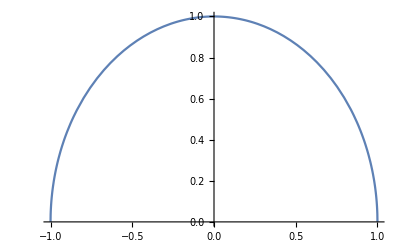

```mathematica
Plot[f[x],{x,a,b}]
```

```mathematica
Px=ParametricPlot3D[{x,0,0},{x,-1,1},PlotStyle->{Thick,Blue}];
Py=ParametricPlot3D[{0,x,0},{x,-1,1},PlotStyle->{Thick,Red}];
Pz=ParametricPlot3D[{0,0,x},{x,-1,1},PlotStyle->{Thick,Green}];
Pr[t_]:=ParametricPlot3D[A[t,x],{x,-1,1},PlotStyle->{Thick}];
```

```mathematica
Manipulate[Show[Px,Py,Pz,Pr[t],Boxed->False,Axes->False],{t,0,2*Pi}]
```

```mathematica
RevolutionPlot3D[f[x],{x,a,b},{t,0,2Pi},RevolutionAxis->{1, 0, 0}, Boxed->False]
```

-Graphics3D-